```mathematica
xi=Table[x,{x,0,1,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
num={0, 1.5, 2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5}
```

{0,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5}

```mathematica
ex=Table[Exp[xi] Sin[xi]]
```

{0.,0.110333,0.242655,0.398911,0.580944,0.790439,1.02885,1.2973,1.59651,1.92667,2.28736}

```mathematica
tab1=Table[{xi[[i]], num[[i]], ex[[i]], ScientificForm[Abs[num[[i]]-ex[[i]]]]}, {i,1,11}]
```

{{0.,0,0.,0.},{0.1,1.5,0.110333,1.38967},{0.2,2.5,0.242655,2.25734},{0.3,3.5,0.398911,3.10109},{0.4,4.5,0.580944,3.91906},{0.5,5.5,0.790439,4.70956},{0.6,6.5,1.02885,5.47115},{0.7,7.5,1.2973,6.2027},{0.8,8.5,1.59651,6.90349},{0.9,9.5,1.92667,7.57333},{1.,10.5,2.28736,8.21264}}

```mathematica
tab2=Prepend[tab1, {"xi", "Num", "Exact", "Error"}]
```

{{xi,Num,Exact,Error},{0.,0,0.,0.},{0.1,1.5,0.110333,1.38967},{0.2,2.5,0.242655,2.25734},{0.3,3.5,0.398911,3.10109},{0.4,4.5,0.580944,3.91906},{0.5,5.5,0.790439,4.70956},{0.6,6.5,1.02885,5.47115},{0.7,7.5,1.2973,6.2027},{0.8,8.5,1.59651,6.90349},{0.9,9.5,1.92667,7.57333},{1.,10.5,2.28736,8.21264}}

```mathematica
Grid[tab2, Frame->All, Spacings->{1, 1}]
```

xi | Num | Exact | Error
0. | 0 | 0. | 0.
0.1 | 1.5 | 0.110333 | 1.38967
0.2 | 2.5 | 0.242655 | 2.25734
0.3 | 3.5 | 0.398911 | 3.10109
0.4 | 4.5 | 0.580944 | 3.91906
0.5 | 5.5 | 0.790439 | 4.70956
0.6 | 6.5 | 1.02885 | 5.47115
0.7 | 7.5 | 1.2973 | 6.2027
0.8 | 8.5 | 1.59651 | 6.90349
0.9 | 9.5 | 1.92667 | 7.57333
1. | 10.5 | 2.28736 | 8.21264

```mathematica
nu=Table[n, {n,2.1,6.4,0.4}]
```

{2.1,2.5,2.9,3.3,3.7,4.1,4.5,4.9,5.3,5.7,6.1}

```mathematica
t=Table[{xi[[i]],nu[[i]]}, {i,1,11}]
```

{{0.,2.1},{0.1,2.5},{0.2,2.9},{0.3,3.3},{0.4,3.7},{0.5,4.1},{0.6,4.5},{0.7,4.9},{0.8,5.3},{0.9,5.7},{1.,6.1}}

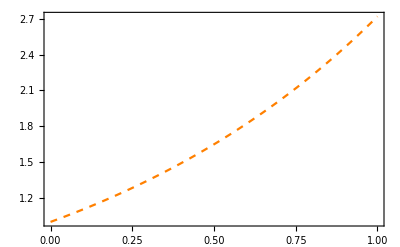

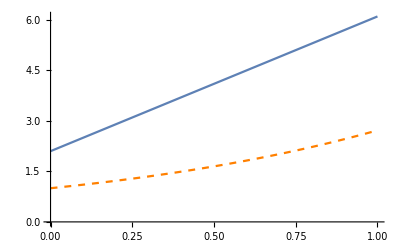

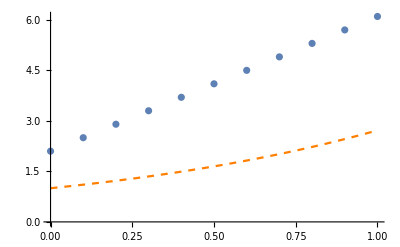

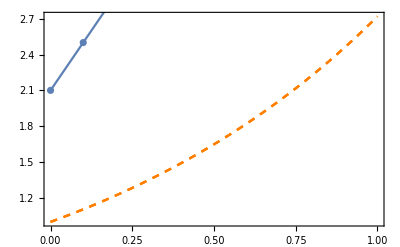

```mathematica
P1=Plot[Exp[x], {x,0,1}, PlotRange->Full, PlotStyle->{Dashed, Orange}, Frame->True]
P2=Show[ListLinePlot[t],P1]
P3=Show[ListPlot[t],P1]
Show[P1, P2, P3]
```